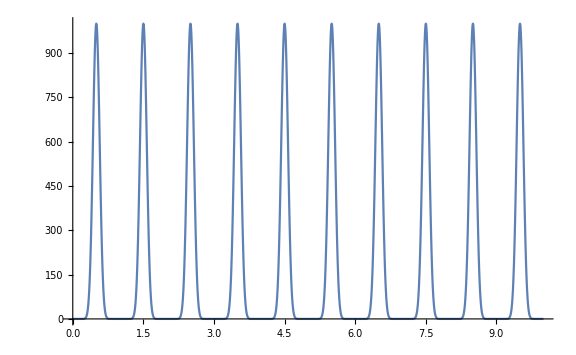

```mathematica
(*setup information*)
h= 1 /100; 
λ=2000;
a0= 1; 
c= 0;
totalTime = 10;
numSteps = totalTime / h;
varC[t_] = 1000*Sin[Pi t]^20;
Plot[varC[t], {t, 0, totalTime}, PlotRange->All, ImageSize->Large]

(*exact solution for changed c*)
```

InterpolatingFunction[…][t]

Cos[20 √5 t]

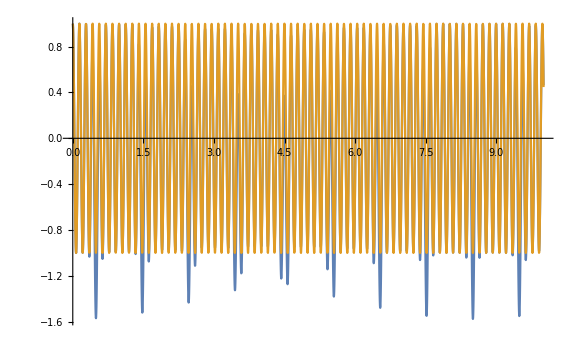

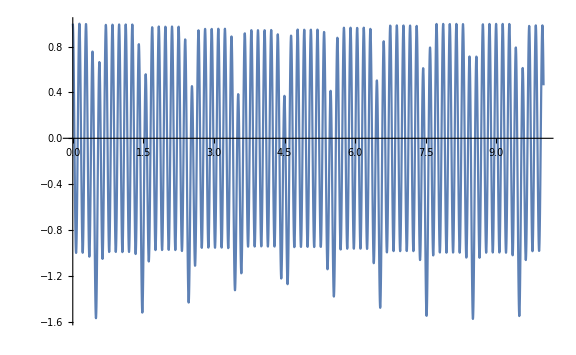

```mathematica
theoSol = NDSolve[{f''[t]+λ f[t]+varC[t]==0,f[0]==a0,f'[0]==0},f[t],{t, 0, totalTime}];
theoα[t_] = (f[t]/.theoSol[[1]]) // FullSimplify
oldα[t_] = (a0 + c / λ) Cos[Sqrt[λ]t] - c / λ
Plot[{theoα[t], oldα[t]}, {t, 0, totalTime}, ImageSize->Large]
Plot[{theoα[t]}, {t, 0, totalTime}, ImageSize->Large]
```

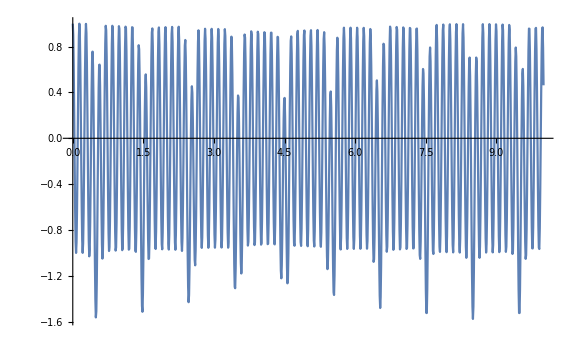

```mathematica
theoList = Table[{n *h, theoα[n* h]}, {n, 0, numSteps}];
ListLinePlot[theoList, PlotRange->All, ImageSize->Large]
```

```mathematica
N
```

N

```mathematica
(*Implicit Euler*)
```

```mathematica
IEM = {{1, -h},{λ h, 1}};
IEw1[n_]= {0,-h varC[n h]};
IEA = Inverse[IEM];
 IEw[n_]= IEA.IEw1[n];
```

```mathematica
IEα = {a0};
IEβ = {0};
timeList = {0};
IEtimeα = {{0, a0}}
For[i=1,i≤numSteps,
a =(IEA[[1,1]] IEα[[i]] + IEA[[1,2]] IEβ[[i]] + IEw[i][[1]])// N;
 b=(IEA[[2,1]] IEα[[i]] + IEA[[2,2]] IEβ[[i]] + IEw[i][[2]])// N;
AppendTo[IEα, a];
AppendTo[IEβ, b];
AppendTo[timeList, i * h];
AppendTo[IEtimeα, {i * h, a}];
i++] ;
```

{{0,1}}

```mathematica
(*Newmark-β*)
NMM = {{1 + h^2 λ β, 0},{λ h / 2, 1}};
NMw1[n_] = {-h^2varC[n h] / 2, - h varC[n h]};
NMM1 ={{1 - h ^2 λ(1/2 - β), h}, {-λ h / 2, 1}}
NMA = Inverse[NMM].NMM1;
NMw[n_] = Inverse[NMM].NMw1[n];
```

{{1+1/5 (-1/2+β),1/100},{-10,1}}

```mathematica
NMα = {a0};
NMβ = {0};
NMtimeα = {{0, a0}};
For[i=1,i≤numSteps,
a =(NMA[[1,1]] NMα[[i]] + NMA[[1,2]] NMβ[[i]] + NMw[i][[1]])/.{β-> 1/4}// N;
 b=(NMA[[2,1]] NMα[[i]] + NMA[[2,2]] NMβ[[i]] + NMw[i][[2]])/.{β-> 1/4}// N;
AppendTo[NMα, a];
AppendTo[NMβ, b];
AppendTo[NMtimeα, {i * h, a}];
i++];
```

```mathematica
(*BDF2*)
BDF2M = {{1, -2h/3}, {2h λ/3, 1}};
BDF2M1 = {{4/3, 0}, {0, 4/3}};
BDF2M2 = {{-1/3, 0}, {0, -1/3}};
BDF2w1[n_] = {0, -2h varC[n * h]/3};
BDF2A1 = Inverse[BDF2M].BDF2M1
BDF2A2 = Inverse[BDF2M].BDF2M2;
BDF2w[n_] = Inverse[BDF2M].BDF2w1[n]
```

{{60/49,2/245},{-800/49,60/49}}

{-2/49 Sin[(n π)/100]^20,-300/49 Sin[(n π)/100]^20}

```mathematica
BDF2α = {a0, IEα[[2]]};
BDF2β = {0, IEβ[[2]]};
BDF2timeα = {{0, a0}, {h, IEα[[2]]}};
For[i=2,i≤numSteps,
a =(BDF2A1[[1,1]] BDF2α[[i]] + BDF2A1[[1,2]] BDF2β[[i]] + BDF2A2[[1,1]] BDF2α[[i-1]] + BDF2A2[[1,2]] BDF2β[[i - 1]] + BDF2w[i][[1]])// N;
 b=(BDF2A1[[2,1]] BDF2α[[i]] + BDF2A1[[2,2]] BDF2β[[i]] + BDF2A2[[2,1]] BDF2α[[i-1]] + BDF2A2[[2,2]] BDF2β[[i - 1]] + BDF2w[i][[2]])// N;
AppendTo[BDF2α, a];
AppendTo[BDF2β, b];
AppendTo[BDF2timeα, {i * h, a}];
i++];
```

```mathematica
(*TRBDF2*)
TRBDF2M = {{1, -γ h}, {γ λ h, 1}};
TRBDF2M1 = {{1, γ h}, {-γ λ h, 1}};
TRBDF2w[n_] = {0, -2  γ * h *  varC[n  h]};
TRBDF2A1 = Inverse[TRBDF2M].TRBDF2M1
TRBDF2w1[n_] = Inverse[TRBDF2M].TRBDF2w[n];

γ2 = (1 - 2γ) / (2 * (1 - γ))
γ3 = (1 - γ2) / (2 * γ)

TRBDF2M2 = {{1, -γ2 * h}, {γ2 * λ * h, 1}};
TRBDF2M3 = {{γ3, 0}, {0, γ3}};
TRBDF2M4 = {{1 - γ3, 0}, {0, 1 - γ3}};
TRBDF2w2[n_] = {0, -γ2 * h * varC[n  h]};

TRBDF2M3 = Inverse[TRBDF2M2].TRBDF2M3;
TRBDF2M4 = Inverse[TRBDF2M2].TRBDF2M4;
TRBDF2w3[n_] = Inverse[TRBDF2M2].TRBDF2w2[n];
```

{{1/(1+γ^2/5)-γ^2/(5 (1+γ^2/5)),γ/(50 (1+γ^2/5))},{-(40 γ)/(1+γ^2/5),1/(1+γ^2/5)-γ^2/(5 (1+γ^2/5))}}

(1-2 γ)/(2 (1-γ))

(1-(1-2 γ)/(2 (1-γ)))/(2 γ)

```mathematica
TRBDF2α = {a0};
TRBDF2β = {0};
TRBDF2timeα = {{0, a0}};
For[i=1,i≤numSteps,
a1 =(TRBDF2A1[[1,1]] TRBDF2α[[i]] + TRBDF2A1[[1,2]] TRBDF2β[[i]] + TRBDF2w1[i][[1]]);
 b1=(TRBDF2A1[[2,1]] TRBDF2α[[i]] + TRBDF2A1[[2,2]] TRBDF2β[[i]] + TRBDF2w1[i][[2]]);
a =(TRBDF2M3[[1,1]] * a1 + TRBDF2M3[[1,2]] * b1 + TRBDF2M4[[1,1]] TRBDF2α[[i]] + TRBDF2M4[[1,2]] TRBDF2β[[i]]  + TRBDF2w3[i][[1]])/.{γ->(1  - Sqrt[2]/ 2)//N};
 b=(TRBDF2M3[[2,1]] * a1 + TRBDF2M3[[2,2]] * b1 + TRBDF2M4[[2,1]] TRBDF2α[[i]] + TRBDF2M4[[2,2]] TRBDF2β[[i]]  + TRBDF2w3[i][[2]])/.{γ->(1  - Sqrt[2]/ 2)//N};
AppendTo[TRBDF2α, a];
AppendTo[TRBDF2β, b];
AppendTo[TRBDF2timeα, {i * h, a}];
i++];
```

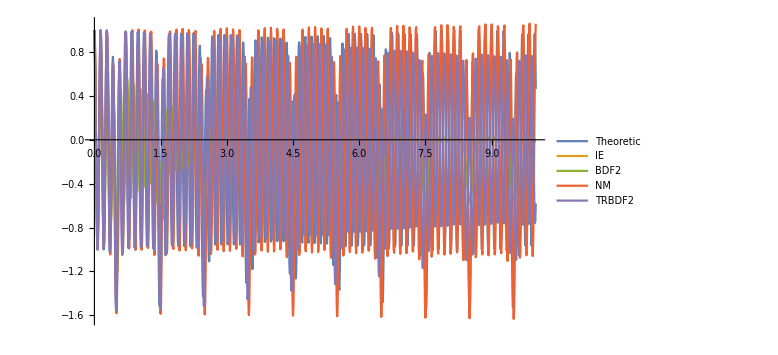

```mathematica
ListLinePlot[{theoList, IEtimeα, BDF2timeα, NMtimeα, TRBDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic", "IE", "BDF2", "NM","TRBDF2"}, ImageSize->Large]
```

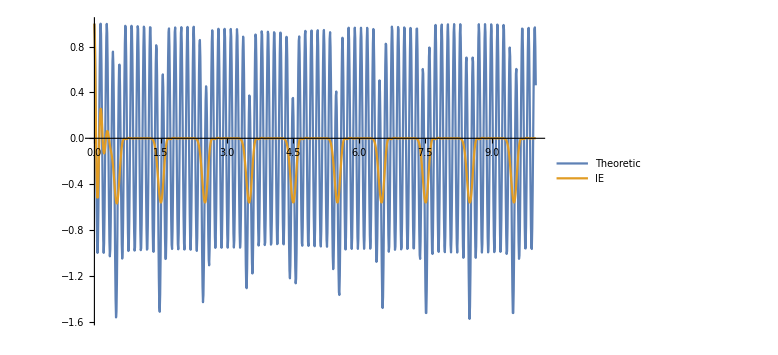

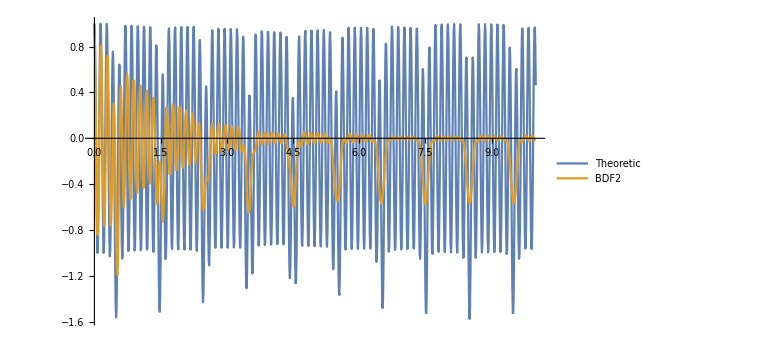

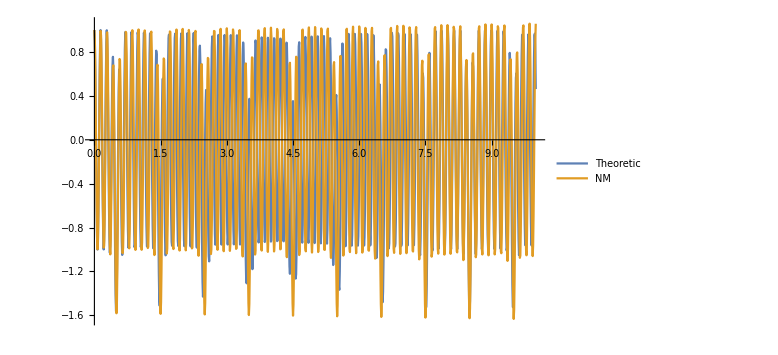

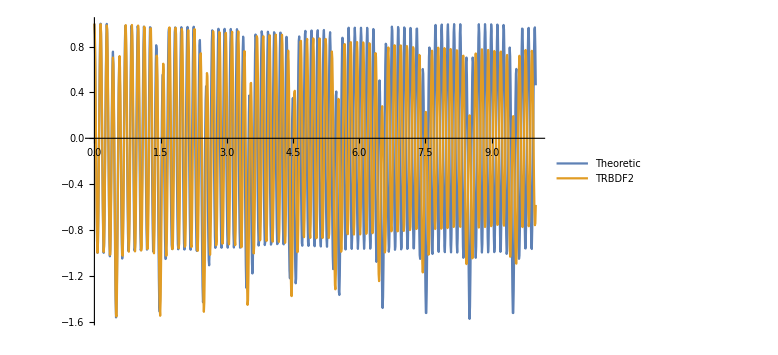

```mathematica
ListLinePlot[{theoList, IEtimeα}, PlotRange->All, PlotLegends->{"Theoretic", "IE"}, ImageSize->Large]
ListLinePlot[{theoList, BDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic", "BDF2"}, ImageSize->Large]
ListLinePlot[{theoList, NMtimeα}, PlotRange->All, PlotLegends->{"Theoretic", "NM"}, ImageSize->Large]
ListLinePlot[{theoList, TRBDF2timeα}, PlotRange->All, PlotLegends->{"Theoretic","TRBDF2"}, ImageSize->Large]
```